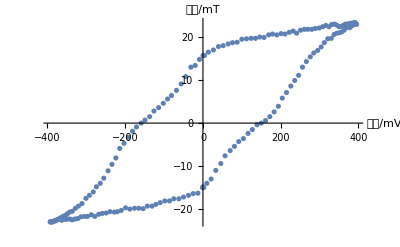

```mathematica
ss=Import["E:\\002课程\\近代物理实验\\数据以及MMA处理代码\\磁滞回线数据\\100%.txt","Table"];
s=Table[{ss[[k,2]],ss[[k,4]]},{k,25,Length[ss]}];

ListPlot[s,AxesLabel->{"电压/mV","磁场/mT"}]
```

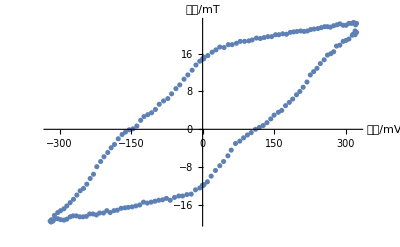

```mathematica
ss=Import["E:\\002课程\\近代物理实验\\数据以及MMA处理代码\\磁滞回线数据\\70%.txt","Table"];
s=Table[{ss[[k,2]],ss[[k,4]]},{k,30,Length[ss]-9}];

ListPlot[s,AxesLabel->{"电压/mV","磁场/mT"}]
```

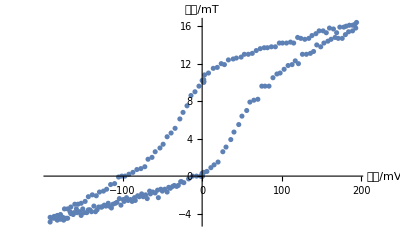

```mathematica
ss=Import["E:\\002课程\\近代物理实验\\数据以及MMA处理代码\\磁滞回线数据\\40%.txt","Table"];
s=Table[{ss[[k,2]],ss[[k,4]]},{k,70,Length[ss]}];

ListPlot[s,AxesLabel->{"电压/mV","磁场/mT"}]
```

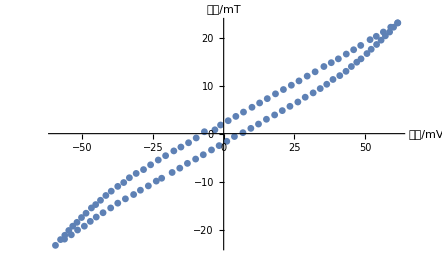

```mathematica
s=Import["E:\\002课程\\近代物理实验\\数据以及MMA处理代码\\磁滞回线数据\\manual recording.txt","Table"];

ListPlot[s,AxesLabel->{"电压/mV","磁场/mT"},PlotMarkers->{Automatic,Small}]
```

{-0.147778,{x→27.6878}}

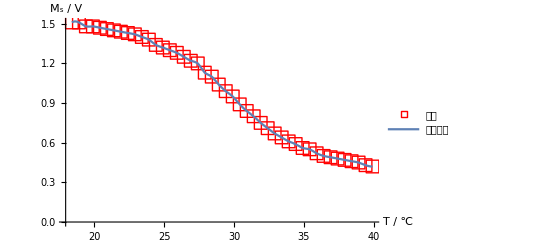

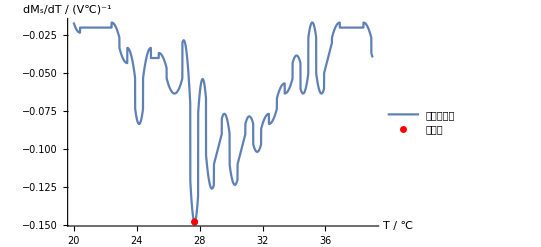

```mathematica
s=Import["E:\\002课程\\近代物理实验\\数据以及MMA处理代码\\居里温度数据.txt","Table"];
f=Interpolation[s];
d=D[f[x],x];
FindMinimum[d,{x,27.1},WorkingPrecision->MachinePrecision]
Show[
ListPlot[s,PlotMarkers->{"□",Medium},PlotStyle->Red,AxesLabel->{"T / ℃","M_s / V"},PlotLegends->{"数据"}],
Plot[f[x],{x,18.41,39.91},PlotLegends->{"插值函数"}]
]
Show[
Plot[d,{x,20,39},PlotLegends->{"模值的导数"}],
ListPlot[{{27.6878,-0.147778}},PlotMarkers->{Automatic, Small},PlotStyle->Red,PlotLegends->{"居里点"}],
AxesLabel->{"T / ℃ ","dM_s/dT / (V:2103)^-1"}
]
```